```mathematica
FName[name_,p_,q_,d_]:=NotebookDirectory[]<>name<>"_"<>ToString[p]<>"_"<>ToString[q]<>If[d>=p+q,"","_"<>ToString[d]];
irrepDims[p_,q_,d_]:=irrepDims[p,q,d]= Import[FName["idempotents/metadata",p,q,d]<>".m"][[1]];
```

```mathematica
(* Transpose a Brauer diagram *)
BT[σ_]:=SortB[B[Sequence@@(FlipPair[#,0]&/@(σ/.B->List))]];
(* Sort the diagram description to make it canonical *)
SortB[σ_]:=Sort@Map[Sort,σ,1];
(*Given the line defined by a pair of vertices, flip the vertices which are located after the wall at level p*)
FlipPair[pair_,p_]:=Sort@(If[Abs[#]>p,-#,#]&/@pair);
(*Generate Walled Brauer Algebra generators*)
WalledBrauerGenerators[p_,q_]:=WalledBrauerGenerators[p,q]=B[Sequence@@#]&/@Map[FlipPair[#,p]&,FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,#,Range[p+q]][[-1]]&/@Table[Range[i-1]~Join~{i+1,i}~Join~Range[i+2,p+q],{i,1,p+q-1}],{2}];
(*Generate Walled Brauer Algebra basis*)
WalledBrauerBasis[p_,q_]:=WalledBrauerBasis[p,q]=(SortB[B[Sequence@@#]])&/@Map[FlipPair[#,p]&,FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,#,Range[p+q]][[-1]]&/@Permutations[Range[p+q]],{2}];
```

```mathematica
(* Contract a Brauer diagram at one fixed position l *)
ContractDiag[diag__,{l_,d_}]:=Module[{new,data},
data=diag/.B->List;
new=Sort@Flatten@Table[If[data[[i]]∩{-l,l}!={},Complement[data[[i]],{-l,l}],{}],{i,1,Length@data}];
If[new=={},d SortB[B[Sequence@@Sort@Table[If[data[[i]]∩{-l,l}!={},Nothing,data[[i]]],{i,1,Length@data}]]], SortB[B[Sequence@@Sort@(Table[If[data[[i]]∩{-l,l}!={},Nothing,data[[i]]],{i,1,Length@data}]~Join~{new})]]]
];
(* Contract a lin. comb. of Brauer diagrams x at one fixed position l *)
ContractOne[x_,{l_,d_}]:=x/.B[lst__]:>ContractDiag[{lst},{l,d}];
(* Contract a lin. comb. of Brauer diagrams x at fixed positions lst *)
Contract[x_,lst_List,d_]:=Fold[ContractOne,x,{lst,ConstantArray[d,Length@lst]}ᵀ];
(* Compute the full trace of a lin. comb. of Brauer diagrams x *)
FullContract[x_,p_,q_,d_]:=Contract[x,Table[i,{i,p+q}],d]/.B[]->1;
(* Same functions, but for 2 registers *)
ContractOne2[x_,{l_,d_}]:=If[l>=p+q+1,x/.(B[lst1__]⊗B[lst2__]:>B[lst1]⊗ContractDiag[{lst2},{l-p+q,d}]),x/.(B[lst1__]⊗B[lst2__]:>ContractDiag[{lst1},{l,d}]⊗B[lst2])];
Contract2[x_,lst_List,d_]:=Fold[ContractOne2,x,{lst,ConstantArray[d,Length@lst]}ᵀ]/.B[]->1;
FullContract2[x_,p_,q_,d_]:=FullContract[Contract2[x,Range[(p+q)],d]/.B[]->1,d];
```

```mathematica
(* Multiply two Brauer algebra diagrams *)
MultiplyPair2[σ1_,σ2_,d_]:=Module[{lst,i,new,pos,σ1n,σ2n},
σ1n=Map[If[#<0,Subscript[b, -#],Subscript[a, #]]&,List@@σ1,{2}];
σ2n=Map[If[#<0,Subscript[b, -#],Subscript[a, #]]&,List@@σ2,{2}];
(* Denote the nodes in the middle layer by x *)
lst=Join[σ1n/.b->x,σ2n/.a->x];
(* Treat each node Subscript[x, i] in the intermediate level *)
Do[
(* Find all edges containing Subscript[x, i] *)
new=lst⟦pos=Position[lst,Subscript[x, i],{2}]⟦All,1⟧⟧;
(* Update the list by removing these edges and adding a new one *)
lst=Append[Delete[lst,List/@pos],DeleteCases[Join@@new,Subscript[x, i]]];
,{i,1,Length[σ1]}
];
(* Output the new Brauer diagram and the normalization factor from the number of loops *)
{B@@SortB@Map[If[TrueQ[First[#]==b],-Part[#,2],Part[#,2]]&,DeleteCases[lst,{}],{2}],d^Count[lst,{}]}
];
(* Multiply two Brauer algebra diagrams *)
MultiplyPair[σ1_,σ2_,d_]:=Times@@MultiplyPair2[σ1,σ2,d];
```

```mathematica
(* Convert integer to a string and padd with 0s *)
Str[i_,max_]:=StringJoin@@(ToString/@IntegerDigits[i,10,IntegerLength@max]);
(* Shorter variable names that also account for symmetry *)
x[λ_,μ_,i_,j_,k_,l_,dB_]:=Symbol["x"<>Str[λ,Length@dB]<>Str[μ,Length@dB]<>StringJoin@@Sort[{Str[i,dB⟦λ⟧]<>Str[k,dB⟦μ⟧],Str[j,dB⟦λ⟧]<>Str[l,dB⟦μ⟧]}]];
```

```mathematica
(* Diagram multiplication tensor *)
prodRule[p_,q_,d_,i_,j_]:=Block[{basis=WalledBrauerBasis[p,q],prod},prod=MultiplyPair2[basis[[i]],basis[[j]],d];{i,j,Position[basis,prod[[1]]][[1,1]]}->prod[[2]]];
mulTensor[p_,q_,d_]:=mulTensor[p,q,d]=SparseArray[Flatten@Table[prodRule[p,q,d,i,j],{i,1,(p+q)!},{j,1,(p+q)!}],{(p+q)!,(p+q)!,(p+q)!}];

(* Diagram contraction tensor *)
contractTensor[p_,q_,d_]:=contractTensor[p,q,d]=Table[FullContract[WalledBrauerBasis[p,q][[i]],p,q,d],{i,1,(p+q)!}];
contractTensor[p_,q_,d_,lst_]:=contractTensor[p,q,d,lst]=Table[(Contract[WalledBrauerBasis[p,q][[i]],lst,d]/.{(B[y__]:>B[Sequence@@({y}/.Flatten[{#[[1]]->#[[2]],-#[[1]]->-#[[2]]}&/@({Complement[Range[p+q],lst],Range[p+q-Length[lst]]}ᵀ)])])})
/.{B[]:>1,B[arg__]:>SparseArray[{Position[WalledBrauerBasis[p-Count[lst,x_/;x<=p],q-Count[lst,x_/;x>p]],B[arg],{1}][[1,1]]}->1,(p+q-Length[lst])!]},{i,1,(p+q)!}]ᵀ;

(* Diagram contraction and adding Id tensor *)
contractIdTensor[p_,q_,d_,lstContract_,lstId_]:=contractIdTensor[p,q,d,lstContract,lstId]=Table[(Contract[WalledBrauerBasis[p,q][[i]],lstContract,d]/.(B[y___]:>SortB@B[Sequence@@({y,Sequence@@({-#,#}&/@lstId)}/.Flatten[{#[[1]]->#[[2]],-#[[1]]->-#[[2]]}&/@({Complement[Range[p+q],Complement[lstContract,lstId]],Range[p+q-Length[lstContract]+Length[lstId]]}ᵀ)])]))/.
{B[]:>1,B[arg__]:>SparseArray[{Position[WalledBrauerBasis[p-Count[Complement[lstContract,lstId],x_/;x<=p],q-Count[Complement[lstContract,lstId],x_/;x>p]],B[arg],{1}][[1,1]]}->1,(p+q-Length[lstContract]+Length[lstId])!]}
,{i,1,(p+q)!}]ᵀ

(* Auxilary tensors *)
mulTensorMatrix[p_,q_,d_]:=mulTensorMatrix[p,q,d]=Flatten[mulTensor[p,q,d],{{1,2},{3}}];
MulContractTensor[p_,q_,d_]:=MulContractTensor[p,q,d]=ArrayReshape[mulTensorMatrix[p,q,d].contractTensor[p,q,d],{(p+q)!,(p+q)!}]
```

```mathematica
(* Operations od 1vecs *)
FullContractVec[vec_,p_,q_,d_]:=(contractTensor[p,q,d].{vec}ᵀ)[[1]]
MultiplyVecs[vec1_,vec2_,p_,q_,d_]:=Flatten[KroneckerProduct[vec1,vec2]].mulTensorMatrix[p,q,d]
MultiplyVecs[vec1_,vec2_,vec3_,p_,q_,d_]:=MultiplyVecs[vec1,MultiplyVecs[vec2,vec3,p,q,d],p,q,d]

(*Define psd constraints and make them symmetric*)
psd[λ_,μ_,p_,q_,d_]:=psd[λ,μ,p,q,d]=Flatten[Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}],{{1,2},{3,4}}];

(*Contract vec, which has the form ∑KroneckerProduct[*,*] on given list of indices *)
Contract2Vec[vec_,p_,q_,d_,lst_]:=contractTensor[p,q,d,Select[lst,#<=(p+q)&]].vec.contractTensor[p,q,d,Select[lst,#>(p+q)&]-(p+q)]ᵀ
Contract2Vec[vec_,p_,q_,d_]:=Contract2Vec[vec,p,q,d,Range[2(p+q)]]
```

```mathematica
(* Realise linear constraints *)
Osys[p_,q_]:=Osys[p,q]=Range[p+q-1];
Psys[p_,q_]:=Psys[p,q]={p+q};
Isys[p_,q_]:=Isys[p,q]=Range[p+q+1,2(p+q)-1];
Fsys[p_,q_]:=Fsys[p,q]={2(p+q)};

Choi[ansatz_,i_,p_,q_,d_]:=If[i<p+q,Expand[If[i==0,Contract2Vec[ansatz,p,q,d],Contract2Vec[ansatz,p,q,d,Osys[p,q][[i;;p+q-1]]~Join~Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q]]]/d^(p+q-i)],ansatz]

TrChoi[ansatz_,i_,p_,q_,d_]:=If[i==0,Print["Error: i should be >0"],Expand[Contract2Vec[ansatz,p,q,d,Osys[p,q][[i;;p+q-1]]~Join~Isys[p,q][[i;;p+q-1]]~Join~Fsys[p,q]]/d^(p+q-i)]]

ChoiTensorId[ansatz_,i_,p_,q_,d_]:=Expand[If[i>=1,
contractIdTensor[p,q,d,Osys[p,q][[i;;p+q-1]],Osys[p,q][[i;;i]]].ansatz.contractTensor[p,q,d,(Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q])-(p+q)]ᵀ,
contractIdTensor[p,q,d,Osys[p,q]~Join~Psys[p,q],Psys[p,q]].ansatz.contractTensor[p,q,d,(Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q])-(p+q)]ᵀ
]/d^(p+q-i)]
```

```mathematica
(* Load blocks *)
blocksLoad[p_,q_,d_]:=blocksLoad[p,q,d]=Import[FName["blocks/blocks",p,q,d]<>".m"]
blocksLoadN[p_,q_,d_]:=blocksLoadN[p,q,d]=N@blocksLoad[p,q,d]

(* Map 2vec to selected blocks *)
vec2ToBlocks[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Sum[vec[[i,j]]KroneckerProduct[blocksLoad[pλ,qλ,d][[i,λ]],blocksLoad[pμ,qμ,d][[j,μ]]],{i,1,(pλ+qλ)!},{j,1,(pμ+qμ)!}]
vec2ToBlocksN[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Sum[vec[[i,j]]KroneckerProduct[blocksLoadN[pλ,qλ,d][[i,λ]],blocksLoadN[pμ,qμ,d][[j,μ]]],{i,1,(pλ+qλ)!},{j,1,(pμ+qμ)!}]

(* Map 2vec to selected blocks *)
vec2ToBlocksBetter[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Flatten[vec].Flatten[Outer[KroneckerProduct,blocksLoad[pλ,qλ,d][[All,λ]],blocksLoad[pμ,qμ,d][[All,μ]],1],{{1,2},{3},{4}}]
vec2ToBlocksBetterN[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Flatten[vec].Flatten[Outer[KroneckerProduct,blocksLoadN[pλ,qλ,d][[All,λ]],blocksLoadN[pμ,qμ,d][[All,μ]],1],{{1,2},{3},{4}}]
```

```mathematica
{p,q,d}={4,1,2};
Print["{p, q, d} = ",{p,q,d}]
Print["Dimensions of simple (𝒜^d)_(p, q)-modules = ",irrepDims[p,q,d]]
```

{p, q, d} = {4,1,2}

Dimensions of simple (𝒜^d)_(p, q)-modules = {1,4,5}

```mathematica
ε=Import[FName["idempotents/elementary",p,q,d]<>".m"];
dimλU=Table[FullContractVec[ε[[λ,1,1]],p,q,d],{λ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
(*Generate the ansatz via eq. (13) in arXiv:2209.02907*)
ansatz=Simplify@ParallelSum[(x[λ,μ,i,j,k,l,irrepDims[p,q,d]]/.guessAnsatz)KroneckerProduct[ε[[λ,i,j]],ε[[μ,k,l]]],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
```

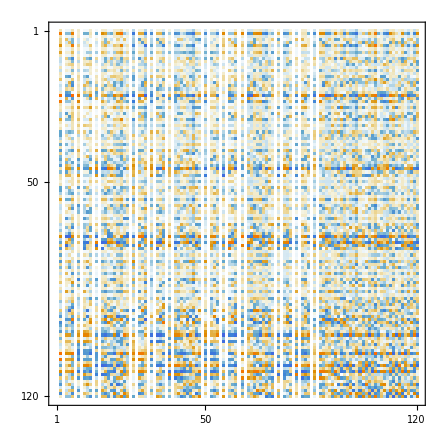

```mathematica
ansatz//MatrixPlot
```

```mathematica
Export[FName["app4_data/ansatz",p,q,d]<>".m",N@ansatz]
```

```mathematica
(*(*Load the above ansatz from the memory*)
ansatz=Import[NotebookDirectory[]<>"app4_data/ansatz_normal_"<>ToString[p]<>"_"<>ToString[q]<>"_"<>ToString[d]<>".m"]/.symSol[p,q,d];*)
```

```mathematica
ansatzNumeric=N@ansatz;
```

```mathematica
ansatzNumeric=Import[FName["app4_data/ansatz",p,q,d]<>".m"];
```

```mathematica
(*Generate the matrix Ω from eq. (18) in arXiv:2209.02907*)
Ω=Sum[1/d^2 1/dimλU[[λ]] KroneckerProduct[ε[[λ,i,j]],ε[[λ,i,j]]],{λ,1,Length[irrepDims[p,q,d]]},{i,1,irrepDims[p,q,d]⟦λ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧}];
```

{0.0416667,0.0416667,0.0416667,0.0416667,0.0138889,0.0138889,0.0138889,0.0138889,0.0104167,0.0104167,0.0104167,0.0104167,0.0104167,0.00208333}

{1/24,1/24,1/24,1/24,1/72,1/72,1/72,1/72,1/96,1/96,1/96,1/96,1/96,1/480}

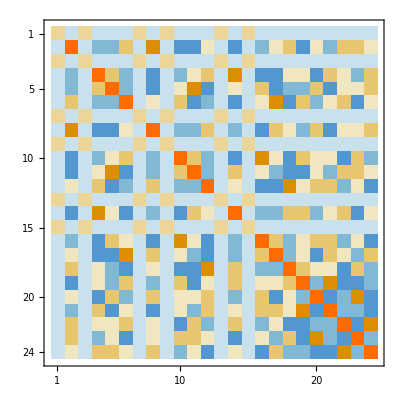

```mathematica
SingularValueList@N@Ω
RootApproximant@%
MatrixPlot@Ω
MatrixForm@Ω
```

```mathematica
Timing[M=MulContractTensor[p,q,d].Ωᵀ.MulContractTensor[p,q,d];]
Timing[ansatzNumericElim=Chop@Expand[ansatzNumeric/.elim];]
Timing[objective=Chop@Total@Expand[Flatten[Mᵀ]*Flatten[ansatzNumericElim]];]
```

{0.214727,Null}

{1.09442,Null}

{16.9948,Null}

```mathematica
(*************************************************)
```

```mathematica
Timing[Chop@Expand@vec2ToBlocksBetterN[eqConstrRaw[[p+q]],2,3,p+q-q,q,p+q-1,0,d];]
Timing[Chop@Expand@vec2ToBlocksN[eqConstrRaw[[p+q]],2,3,p+q-q,q,p+q-1,0,d];]
```

{66.3024,Null}

{69.3575,Null}

```mathematica
eqConstrRaw=Table[PrintTemporary[i];Chop[TrChoi[ansatzNumeric,i,p,q,d]-ChoiTensorId[ansatzNumeric,i-1,p,q,d]],{i,1,p+q}];
```

```mathematica
Timing[eqConstr=Chop@Flatten[{Choi[ansatzNumeric,0,p,q,d]-1}~Join~eqConstrRaw[[1;;2]]~Join~Table[PrintTemporary[i];Table[PrintTemporary[{λ,μ,irrepDims[i-q,q,d]⟦λ⟧*irrepDims[i-1,0,d]⟦μ⟧}];Expand@vec2ToBlocksBetterN[eqConstrRaw[[i]],λ,μ,i-q,q,i-1,0,d],{λ,1,Length[irrepDims[i-q,q,d]]},{μ,1,Length[irrepDims[i-1,0,d]]}],{i,3,p+q}]];]
```

{653.537,Null}

```mathematica
eqConstr=Import[FName["app4_data/eq",p,q,d]<>"_exact.m"];
```

```mathematica
eqConstrExact=Import[FName["app4_data/eq",p,q,d]<>"_exact.m"];
```

```mathematica
eqConstrExact/.guessAnsatz//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Solve[(#==0)&/@Union@FullSimplify@Union@(eqConstrExact/.guessAnsatz)]
```

{{a1→-(√5)/4,a2→(√(3/2))/2,a3→-1/(2 √2),a4→-1/(2 √6),a5→-1/(4 √3)}}

```mathematica
(***************************************)
```

```mathematica
elim={};
```

```mathematica
psdElim[λ_,μ_,p_,q_,d_]:=Chop@Expand[psd[λ,μ,p,q,d]/.elim];
```

```mathematica
psdConstr=Flatten@Table[VectorGreaterEqual[{psdElim[λ,μ,p,q,d],0},{"SemidefiniteCone",irrepDims[p,q,d]⟦λ⟧*irrepDims[p,q,d]⟦μ⟧ }],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
vars=Variables@Table[psdElim[λ,μ,p,q,d],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
Length@%
```

228

```mathematica
(*vars=Union@Flatten@Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];*)
```

```mathematica
objective=(3 x111111)/2+x221111+2 x221122+2 x221133+2 x221144+x222222+2 x222233+2 x222244+x223333+2 x223344+x224444+x331111/2+x331122+x331133+x331144+x331155+x332222/2+x332233+x332244+x332255+x333333/2+x333344+x333355+x334444/2+x334455+x335555/2/.guessAnsatz
```

1

```mathematica
sol=Dispatch@SemidefiniteOptimization[-objective,psdConstr~Join~((#==0)&/@(eqConstr/.elim)),vars];
```

```mathematica
objective/.sol//Chop
```

1.

```mathematica
Sort@Abs@Chop[vars/.sol,10^-5]
Length@%
```

{0.00327364,0.00601272,0.00654728,0.00655713,0.00896651,0.00926767,0.0100223,0.0104149,0.0104154,0.0104154,0.0104154,0.0104154,0.0104182,0.0113402,0.0120264,0.0126787,0.0130727,0.0130946,0.0138945,0.0170078,0.0170078,0.017924,0.0180386,0.0180392,0.0180393,0.0180394,0.0180394,0.0180394,0.0180395,0.0180395,0.0180395,0.0180395,0.0180401,0.0180401,0.0180402,0.018041,0.018527,0.018532,0.0208318,0.0226806,0.0240527,0.0253545,0.0261846,0.027795,0.0294584,0.0294606,0.0312437,0.0312439,0.0312439,0.0312449,0.0312453,0.0312453,0.0312455,0.0312455,0.0312455,0.0312455,0.0312463,0.0312465,0.0312465,0.0312469,0.0312474,0.0312479,0.0312481,0.0312484,0.0312484,0.0312484,0.0312484,0.0312484,0.0312484,0.0312493,0.0320752,0.0340157,0.0340157,0.0358665,0.0405213,0.0416605,0.0416635,0.0453531,0.0465779,0.0465779,0.0507125,0.0510272,0.0510272,0.054116,0.054116,0.0541166,0.0541184,0.0541187,0.0541187,0.0541187,0.0541187,0.0541187,0.0541187,0.0541187,0.0541193,0.0541205,0.0541212,0.0541212,0.0541215,0.0541215,0.0541221,0.0541221,0.0541221,0.0541221,0.0541221,0.0541221,0.0541233,0.0541236,0.0541236,0.0541236,0.0541239,0.0541242,0.0555642,0.0589142,0.0589169,0.0589169,0.0589169,0.0589172,0.0589211,0.065871,0.065871,0.0701541,0.0721633,0.0721633,0.0740812,0.078701,0.0806811,0.0883842,0.0937327,0.0937364,0.0937364,0.0937364,0.0937364,0.0937364,0.0937374,0.0937374,0.0937406,0.0937411,0.0937411,0.0937416,0.0937422,0.0937422,0.0937422,0.0937422,0.0937422,0.0937422,0.0937422,0.0937432,0.0937453,0.0937453,0.0937458,0.0937458,0.0937458,0.0937458,0.0937458,0.0937458,0.0937463,0.09375,0.0937516,0.0937547,0.102042,0.102043,0.102047,0.102048,0.102048,0.102048,0.102053,0.102054,0.102054,0.102054,0.114092,0.1141,0.121528,0.124991,0.124994,0.129624,0.13078,0.13194,0.142353,0.148142,0.157415,0.162032,0.162356,0.162358,0.162365,0.162366,0.162366,0.162366,0.162366,0.162372,0.162372,0.162373,0.162373,0.162373,0.162373,0.162373,0.16238,0.162382,0.162382,0.162382,0.164352,0.176744,0.176752,0.176753,0.176753,0.17676,0.176761,0.176763,0.176763,0.176768,0.180395,0.192422,0.197627,0.197627,0.216496,0.281226,0.281237,0.281239,0.281253,0.281255,0.281258,0.306144,0.30616,0.306172,0.312476,0.333308,0.34231,0.375009}

228

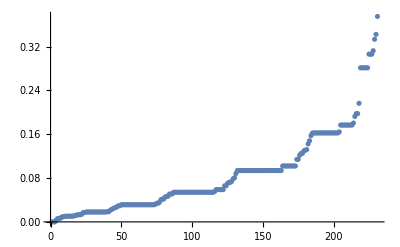

```mathematica
Abs@Chop[vars/.sol,10^-5];
ListPlot@Sort@%
```

```mathematica
Flatten@Position[Chop[vars/.sol,10^-5],0];
zeroes=Rule@@@Transpose@{vars⟦%⟧,ConstantArray[0,Length@%]};
```

```mathematica
zeroes
```

{x332323→0,x333232→0,x333333→0}

```mathematica
(* Guess for blocks p=4, q=1 *)
(*Block 2,3*)
v[2,3]=({{0, 0, 0, -(√15)/12, -(√5)/4, 0, 0, 0, (√(3/2))/2, -1/(2 √2), 0, 0, 0, -1/(6 √2), -1/(2 √6), 0, 0, 0, -1/12, -1/(4 √3)}, {(√15)/12, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(8 √2)/12, 0, 0, 0, 0, 1/12, 0, 0, 0, 0}, {0, 0, 0, -1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√15)/4, 0}, {0, 0, 0, (√15)/12, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(2 √2)/3, 0, 0, 0, 0, 1/12, 0}, {1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(√15)/4, 0, 0, 0, 0}});
λs[2,3]={1,1/6,1/6,1/6,1/6};
B[2,3]=v[2,3]ᵀ.DiagonalMatrix[λs[2,3]].v[2,3]//FullSimplify;
(*Block 3,3*)
v[3,3]=({{3/8, (√3)/8, 0, (√3)/8, -1/8, -(√3)/8, 3/8, 0, 1/24, 1/(8 √3), 0, 0, 0, -1/(3 √2), -1/(√6), -(√3)/8, -1/8, 0, 3/8, -(√3)/8, -1/8, (√3)/8, 0, -1/(8 √3), -1/8}, {0, 0, 0, 0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0}, {0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0, 0, 0, 0}});
λs[3,3]={2,1/6,1/6};
B[3,3]=v[3,3]ᵀ.DiagonalMatrix[λs[3,3]].v[3,3]//FullSimplify;
(*Block 2,2*)
v[2,2]=({{0, -1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√15)/4, 0, 0}, {0, -(√(5/3))/4, 0, 0, 0, 0, 0, 0, 0, (2 √2)/3, 0, 0, 0, -1/12, 0, 0}});
λs[2,2]={1/12,1/12};
B[2,2]=v[2,2]ᵀ.DiagonalMatrix[λs[2,2]].v[2,2]//FullSimplify;
(*Block 3,2*)
v[3,2]=({{0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0, 0}});
λs[3,2]={1/12};
B[3,2]=v[3,2]ᵀ.DiagonalMatrix[λs[3,2]].v[3,2]//FullSimplify;
B[1,1]=ConstantArray[0,{1,1}];
B[2,1]=ConstantArray[0,{4,4}];
B[3,1]=ConstantArray[0,{5,5}];
B[1,2]= ({{0, 0, 0, 0}, {0, 1/12, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
B[1,3]= ({{1/6, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 1/6, 0}, {0, 0, 0, 0, 0}});
```

```mathematica
guessAnsatz=Dispatch@Flatten@Table[Rule@@@Transpose@{Flatten[Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}]],Flatten[B[λ,μ]]},{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
blocks=Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]]/.elim/.sol,{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
blocks=Flatten[blocks,{{1},{2},{3,4},{5,6}}];
MatrixForm@Map[MatrixForm,blocks,{2}]
```

((0) | (0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.166734 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.304254 | 0 | 0 | 0 | -0.215089 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.304254 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.888974 | 0 | 0 | 0 | -0.0786856 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.215089 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0786856 | 0 | 0 | 0 | 0.944412 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0.33354 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.60855 | 0 | 0 | 0 | 0 | -0.430398 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.58327 | 2.16474 | 0 | 0 | 0 | -2.37153 | 1.3691 | 0 | 0 | 0 | -0.152145 | 0.790453 | 0 | 0 | 0 | -0.107598 | 0.558934
0 | 0 | 0 | 2.16474 | 3.74972 | 0 | 0 | 0 | -4.10772 | 2.37153 | 0 | 0 | 0 | 0.790453 | 1.3692 | 0 | 0 | 0 | 0.558934 | 0.968173
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2.37153 | -4.10772 | 0 | 0 | 0 | 4.50011 | -2.59795 | 0 | 0 | 0 | -0.86596 | -1.49993 | 0 | 0 | 0 | -0.612326 | -1.06061
0 | 0 | 0 | 1.3691 | 2.37153 | 0 | 0 | 0 | -2.59795 | 1.49989 | 0 | 0 | 0 | 0.499926 | 0.86596 | 0 | 0 | 0 | 0.353501 | 0.612326
-0.60855 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.77771 | 0 | 0 | 0 | 0 | -0.156872 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.152145 | 0.790453 | 0 | 0 | 0 | -0.86596 | 0.499926 | 0 | 0 | 0 | 1.94438 | 0.288632 | 0 | 0 | 0 | -0.0392837 | 0.204094
0 | 0 | 0 | 0.790453 | 1.3692 | 0 | 0 | 0 | -1.49993 | 0.86596 | 0 | 0 | 0 | 0.288632 | 0.499962 | 0 | 0 | 0 | 0.204094 | 0.353527
-0.430398 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.156872 | 0 | 0 | 0 | 0 | 1.88898 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.107598 | 0.558934 | 0 | 0 | 0 | -0.612326 | 0.353501 | 0 | 0 | 0 | -0.0392837 | 0.204094 | 0 | 0 | 0 | 1.97222 | 0.144316
0 | 0 | 0 | 0.558934 | 0.968173 | 0 | 0 | 0 | -1.06061 | 0.612326 | 0 | 0 | 0 | 0.204094 | 0.353527 | 0 | 0 | 0 | 0.144316 | 0.249981)
(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.222324 | 0 | 0 | 0 | 0.157136 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.384902 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.157136 | 0 | 0 | 0 | 0.111212 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.272167 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.384902 | 0 | 0 | 0 | -0.272167 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.66677 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (3.37506 | 1.94847 | 0 | 1.94856 | -1.12489 | -1.94839 | 3.37485 | 0 | 0.374975 | 0.649479 | 0 | 0 | 0 | -2.12113 | -3.67392 | -1.94859 | -1.12495 | 0 | 3.37504 | -1.94839 | -1.12491 | 1.94847 | 0 | -0.649454 | -1.12489
1.94847 | 1.12491 | 0 | 1.12494 | -0.649425 | -1.12484 | 1.94839 | 0 | 0.216481 | 0.374958 | 0 | 0 | 0 | -1.22457 | -2.12103 | -1.12495 | -0.649465 | 0 | 1.94848 | -1.12485 | -0.649425 | 1.12491 | 0 | -0.374944 | -0.649425
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.94856 | 1.12494 | 0 | 1.12506 | -0.649483 | -1.12489 | 1.94846 | 0 | 0.216474 | 0.374992 | 0 | 0 | 0 | -1.22465 | -2.12122 | -1.125 | -0.649486 | 0 | 1.94859 | -1.12495 | -0.649454 | 1.12494 | 0 | -0.374981 | -0.649483
-1.12489 | -0.649425 | 0 | -0.649483 | 0.374981 | 0.649392 | -1.12484 | 0 | -0.124985 | -0.216474 | 0 | 0 | 0 | 0.707002 | 1.22465 | 0.649457 | 0.374946 | 0 | -1.12495 | 0.649465 | 0.374927 | -0.649425 | 0 | 0.216473 | 0.374981
-1.94839 | -1.12484 | 0 | -1.12489 | 0.649392 | 1.56936 | -1.94827 | 0 | -0.21647 | -0.374939 | 0.314215 | 0 | 0 | 1.22451 | 2.12092 | 1.12491 | 0.649425 | 0 | -1.94838 | 1.12479 | -0.120267 | -1.12484 | 0 | 0.374925 | 0.649392
3.37485 | 1.94839 | 0 | 1.94846 | -1.12484 | -1.94827 | 3.37472 | 0 | 0.374956 | 0.649447 | 0 | 0 | 0 | -2.12102 | -3.67373 | -1.94847 | -1.12491 | 0 | 3.37487 | -1.9483 | -1.12484 | 1.94839 | 0 | -0.649421 | -1.12484
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.374975 | 0.216481 | 0 | 0.216474 | -0.124985 | -0.21647 | 0.374956 | 0 | 0.486255 | 0.0721527 | 0 | 0 | 0 | 0.0785673 | -0.408188 | -0.216492 | -0.124985 | 0 | 0.374981 | -0.216473 | -0.124979 | 0.216481 | 0 | -0.84185 | -0.124985
0.649479 | 0.374958 | 0 | 0.374992 | -0.216474 | -0.374939 | 0.649447 | 0 | 0.0721527 | 0.125019 | 0 | 0 | 0 | -0.408188 | -0.707054 | -0.374977 | -0.216482 | 0 | 0.649483 | -0.374981 | -0.216471 | 0.374958 | 0 | -0.124985 | -0.216474
0 | 0 | 0 | 0 | 0 | 0.314215 | 0 | 0 | 0 | 0 | 0.222385 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.544237 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.12113 | -1.22457 | 0 | -1.22465 | 0.707002 | 1.22451 | -2.12102 | 0 | 0.0785673 | -0.408188 | 0 | 0 | 0 | 1.55549 | 2.30906 | 1.22463 | 0.707006 | 0 | -2.12116 | 1.22456 | 0.706971 | -1.22457 | 0 | -0.136083 | 0.707002
-3.67392 | -2.12103 | 0 | -2.12122 | 1.22465 | 2.12092 | -3.67373 | 0 | -0.408188 | -0.707054 | 0 | 0 | 0 | 2.30906 | 3.9997 | 2.12114 | 1.22458 | 0 | -3.67406 | 2.12116 | 1.22452 | -2.12103 | 0 | 0.707002 | 1.22465
-1.94859 | -1.12495 | 0 | -1.125 | 0.649457 | 1.12491 | -1.94847 | 0 | -0.216492 | -0.374977 | 0 | 0 | 0 | 1.22463 | 2.12114 | 1.12502 | 0.64949 | 0 | -1.94858 | 1.12491 | 0.649465 | -1.12495 | 0 | 0.374962 | 0.649457
-1.12495 | -0.649465 | 0 | -0.649486 | 0.374946 | 0.649425 | -1.12491 | 0 | -0.124985 | -0.216482 | 0 | 0 | 0 | 0.707006 | 1.22458 | 0.64949 | 0.374969 | 0 | -1.12496 | 0.649432 | 0.374946 | -0.649465 | 0 | 0.216474 | 0.374946
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.37504 | 1.94848 | 0 | 1.94859 | -1.12495 | -1.94838 | 3.37487 | 0 | 0.374981 | 0.649483 | 0 | 0 | 0 | -2.12116 | -3.67406 | -1.94858 | -1.12496 | 0 | 3.37509 | -1.94846 | -1.1249 | 1.94848 | 0 | -0.649465 | -1.12495
-1.94839 | -1.12485 | 0 | -1.12495 | 0.649465 | 1.12479 | -1.9483 | 0 | -0.216473 | -0.374981 | 0 | 0 | 0 | 1.22456 | 2.12116 | 1.12491 | 0.649432 | 0 | -1.94846 | 1.12492 | 0.649399 | -1.12485 | 0 | 0.374946 | 0.649465
-1.12491 | -0.649425 | 0 | -0.649454 | 0.374927 | -0.120267 | -1.12484 | 0 | -0.124979 | -0.216471 | -0.544237 | 0 | 0 | 0.706971 | 1.22452 | 0.649465 | 0.374946 | 0 | -1.1249 | 0.649399 | 1.70823 | -0.649425 | 0 | 0.216463 | 0.374927
1.94847 | 1.12491 | 0 | 1.12494 | -0.649425 | -1.12484 | 1.94839 | 0 | 0.216481 | 0.374958 | 0 | 0 | 0 | -1.22457 | -2.12103 | -1.12495 | -0.649465 | 0 | 1.94848 | -1.12485 | -0.649425 | 1.12491 | 0 | -0.374944 | -0.649425
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.649454 | -0.374944 | 0 | -0.374981 | 0.216473 | 0.374925 | -0.649421 | 0 | -0.84185 | -0.124985 | 0 | 0 | 0 | -0.136083 | 0.707002 | 0.374962 | 0.216474 | 0 | -0.649465 | 0.374946 | 0.216463 | -0.374944 | 0 | 1.45834 | 0.216473
-1.12489 | -0.649425 | 0 | -0.649483 | 0.374981 | 0.649392 | -1.12484 | 0 | -0.124985 | -0.216474 | 0 | 0 | 0 | 0.707002 | 1.22465 | 0.649457 | 0.374946 | 0 | -1.12495 | 0.649465 | 0.374927 | -0.649425 | 0 | 0.216473 | 0.374981))

```mathematica
MatrixForm@Map[MatrixForm,Chop[Map[Eigenvalues,blocks,{2}],10^-5],{2}]
```

((0) | (1
0
0
0) | (2
2
0
0
0)
(0
0
0
0) | (1.00016
0.99986
0.000100415
0
0
0
0
0
0
0
0
0
0
0
0
0) | (11.9993
2.0003
2.
1.99994
1.99973
0.000216443
0.000200831
0.0000931822
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0) | (1.0001
0.000100415
0.000100415
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (23.9982
1.99994
1.99985
0.000455291
0.000216638
0.000200831
0.000199831
0.0001782
0.000058055
0.0000534267
0.0000351833
0
0
0
0
0
0
0
0
0
0
0
0
0
0))

```mathematica
(**)
```

((0) | (0.0833333
0
0
0) | (1/6
1/6
0
0
0)
(0
0
0
0) | (0.0833193
0.0833137
0.0000179256
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0.999873
0.166696
0.166688
0.166684
0.166667
0.0000386387
0.0000358513
0.0000166359
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0) | (0.0833126
0.0000179256
0.0000179256
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1.99968
0.166688
0.166687
0.0000812744
0.000038673
0.0000358513
0.0000356731
0.0000318115
0.0000103646
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0))

```mathematica
irrepDims[p,q,d]
```

{1,3,2}

```mathematica
A=Chop[ansatzNumeric/.sol];
```

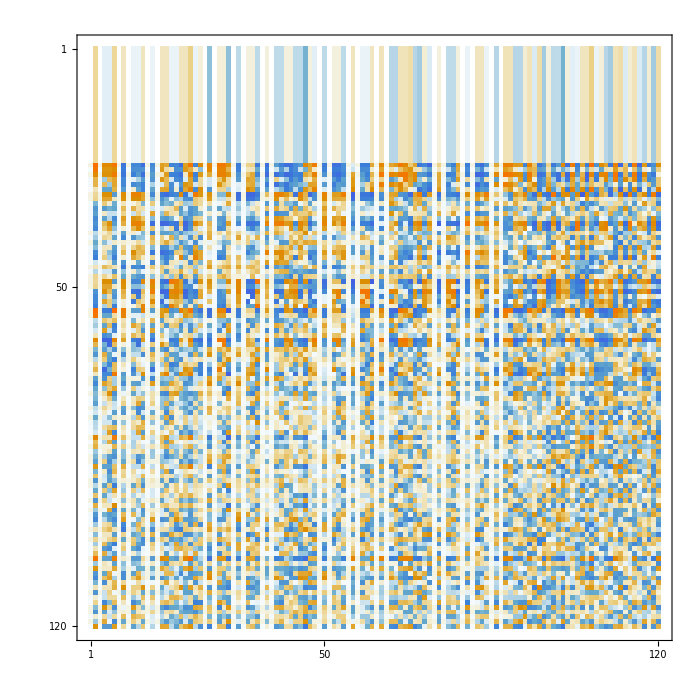

```mathematica
MatrixPlot@A
```